```mathematica
model1=
```

```mathematica
model2=
```

```mathematica
model3=
```

```mathematica
model4=
```

```mathematica
model5=
```

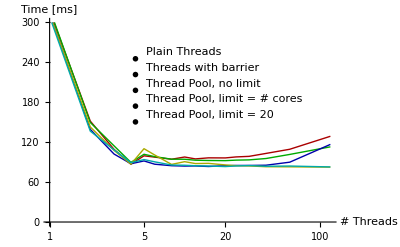

```mathematica
workers = {1,2,3,4,5,6,8,10,12,15,20,24,30,40,60,120};
ToPoint[data_]:=(#/.{x_,t_}:>({x,#}&)/@t)&/@data;
ToMedian[data_]:=(#1/.{x_,t_}:>{x, TrimmedMean[t,0.3]})&/@data;
ToSeconds[data_]:=(#/.{x_,t_}:>{x, #/1000000&/@t})&/@data;
models={model1,model2,model3,model4,model5};
models=Transpose@{workers, #}&/@models;
models=ToSeconds/@models;
Needs["PlotLegends`"]
legend=Sequence[PlotLegend->{"Plain Threads","Threads with barrier","Thread Pool, no limit","Thread Pool, limit = # cores","Thread Pool, limit = 20"},LegendShadow->None,LegendPosition->{-0.4,-0.05},LegendTextSpace->8,LegendSize->{0.8,0.5}];
options=Sequence[Joined->True,PlotStyle-> Darker/@{Red,Green,Blue,Yellow,Cyan},AxesLabel->{"# Threads","Time [ms]"}];
ModelPlot[model_,range_,opts__]:=ListLogLinearPlot[model,PlotRange->range,opts];
ListLogLinearPlot[First[ToPoint/@models]];
ModelPlot[ToMedian/@models,{{0,120},{0,300}},options,legend]
ModelPlot[ToMedian/@models,{{2,120},{80,130}},options]
```